```mathematica
(* =====================================================================
   0. Setup — 载入数据 + EKV 常量 + 反求函数 + 工作点
   ===================================================================== *)
dataDir = "D:\\tsmcN40_lookup";
scriptDir = FileNameJoin[{dataDir, "mathematica"}];
Get[FileNameJoin[{scriptDir, "tsmcN40_lookup.wl"}]];
Get[FileNameJoin[{scriptDir, "ekv_extract.wl"}]];

nch = LoadTsmcN40[FileNameJoin[{dataDir, "nch_tt.h5"}]];

UT = 1.380649*^-23*300./1.602176634*^-19;   (* kT/q @300K *)
L = 0.1; VDS = 0.55; VSB = 0.; rho = 0.6;   (* VDS=VDD/2 *)
vgs = nch["VGS"]; vdsVec = Select[nch["VDS"], # >= 0.3 &];

(* 反求正常化电荷 q: x = 2(q-1) + ln(q) *)
invq[x_?NumericQ] := Module[{f}, f[q_?NumericQ] := 2 (q - 1) + Log[q] - x;
   q /. Quiet@FindRoot[f[q], {q, 0.5}]];
invq[x_List] := invq /@ x;
```

```mathematica
(* =====================================================================
   1. 提取: 单点 XTRACT 输出
   ===================================================================== *)
y = XTRACT[nch, L, VDS, VSB, rho];
Grid[{{"VDS", y[[1]], "V"}, {"n", y[[2]]}, {"VT", y[[3]], "V"},
   {"JS", y[[4]]*1.*^6, "uA/um"}, {"dn/dVDS", y[[5]]}, {"dVT/dVDS", y[[6]]},
   {"dlogJS/dVDS", y[[7]]}}, Frame -> All, Spacings -> {2, 1}]
```

VDS | 0.55 | V
n | 1.27533 | 
VT | 0.474355 | V
JS | 3.5854 | uA/um
dn/dVDS | 0.0000360898 | 
dVT/dVDS | -0.0282724 | 
dlogJS/dVDS | 0.227475 |

```mathematica
(* =====================================================================
   2. 重建: 消息就绪（全局变量供 3/4节图引用）
   黑点 = 参考工作点 gm/ID = rho*max(lookup)
   ===================================================================== *)
n = y[[2]]; VT = y[[3]]; JS = y[[4]];
q = 10.^Subdivide[-3, 1, 199];
VGSekv = n*UT*(2 (q - 1) + Log[q]) + VT;
JDekv = (q^2 + q)*JS;
gmIDekv = 1/(n*UT (1 + q));
JDLut = lookup[nch, "ID_W", "L", L, "VGS", vgs, "VDS", VDS, "VSB", VSB];
gmIDLut = lookup[nch, "GM_ID", "L", L, "VGS", vgs, "VDS", VDS, "VSB", VSB];
ref = rho*Max[gmIDLut];
VGSr = Interpolation[Transpose[{Reverse[gmIDekv], Reverse[VGSekv]}],
   InterpolationOrder -> 1][ref];
JDr = Interpolation[Transpose[{VGSekv, JDekv}], InterpolationOrder -> 1][VGSr];
Row[{"VGSr=", VGSr, " V, JDr=", JDr*1.*^6, " uA/um"}]
```

VGSr=0.439015 V, JDr=3.98583 uA/um

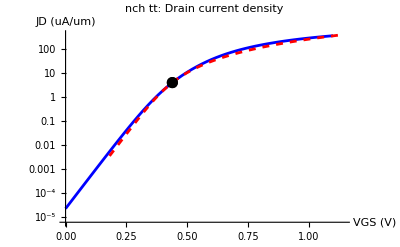

```mathematica
(* =====================================================================
   3. 电流密度 JD vs VGS — 查表 vs 基本 EKV
   黑点 = 参考工作点 gm/ID = rho*max(lookup)
   ===================================================================== *)
Show[ListLogPlot[{Transpose[{vgs, Abs[JDLut]*1.*^6}],
   Transpose[{VGSekv, JDekv*1.*^6}]}, Joined -> True,
  PlotStyle -> {Blue, {Red, Dashed}}, PlotRange -> All,
  AxesLabel -> {"VGS (V)", "JD (uA/um)"}, PlotLabel -> "nch tt: Drain current density",
  GridLines -> Automatic],
 ListLogPlot[{{VGSr, JDr*1.*^6}}, PlotStyle -> {Black, PointSize[.02]}]]
```

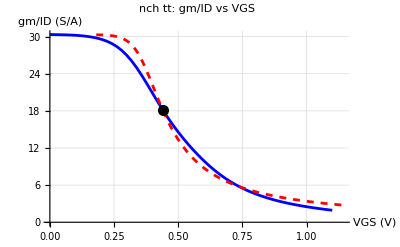

```mathematica
(* =====================================================================
   4. 跨导效率 gm/ID vs VGS — 查表 vs 基本 EKV
   ===================================================================== *)
ListPlot[{Transpose[{vgs, gmIDLut}], Transpose[{VGSekv, gmIDekv}]},
 Joined -> True, PlotStyle -> {Blue, {Red, Dashed}}, PlotRange -> All,
 Epilog -> {Black, PointSize[.02], Point[{VGSr, ref}]},
 AxesLabel -> {"VGS (V)", "gm/ID (S/A)"}, PlotLabel -> "nch tt: gm/ID vs VGS",
 GridLines -> Automatic]
```

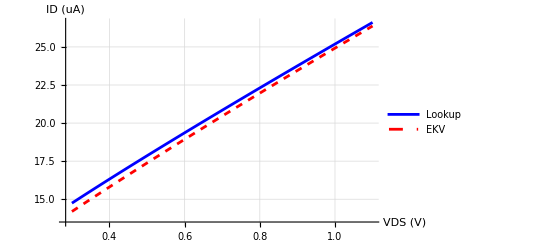

```mathematica
(* =====================================================================
   5. ID vs VDS — 固定 VGS=0.4V 扫 VDS，检验重建
   ===================================================================== *)
With[{yy = XTRACT[nch, L, vdsVec, VSB, rho]},
  nV = yy[[All, 2]]; vtV = yy[[All, 3]]; jsV = yy[[All, 4]];
  qV = invq[((0.4 - vtV)/nV)/UT];
  idEkv = nch["W"]*jsV*(qV^2 + qV);
  idLut = lookup[nch, "ID", "L", L, "VGS", 0.4, "VDS", vdsVec, "VSB", VSB];
  ListLinePlot[{Transpose[{vdsVec, idLut*1.*^6}], Transpose[{vdsVec, idEkv*1.*^6}]},
   PlotStyle -> {Blue, {Red, Dashed}}, PlotLegends -> {"Lookup", "EKV"},
   AxesLabel -> {"VDS (V)", "ID (uA)"}, GridLines -> Automatic]
]
```

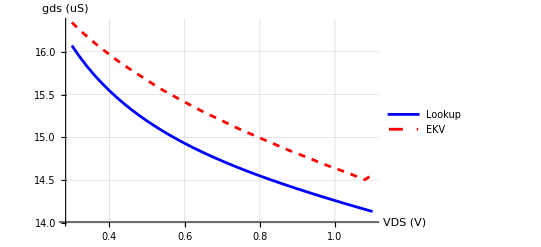

```mathematica
(* =====================================================================
   6. gds vs VDS — 同上，导数项: -gm(dVT/dVDS + x dn/dVDS) + ID dlogJS/dVDS
   ===================================================================== *)
With[{yy = XTRACT[nch, L, vdsVec, VSB, rho]},
  nV = yy[[All, 2]]; vtV = yy[[All, 3]]; jsV = yy[[All, 4]];
  xV = ((0.4 - vtV)/nV)/UT;
  qV = invq[xV];
  gdsEkv = -nch["W"]*jsV/(nV*UT)*qV*(yy[[All, 6]] + xV*yy[[All, 5]]) +
    nch["W"]*jsV*(qV^2 + qV)*yy[[All, 7]];
  gdsLut = lookup[nch, "GDS", "L", L, "VGS", 0.4, "VDS", vdsVec, "VSB", VSB];
  ListLinePlot[{Transpose[{vdsVec, gdsLut*1.*^6}], Transpose[{vdsVec, gdsEkv*1.*^6}]},
   PlotStyle -> {Blue, {Red, Dashed}}, PlotLegends -> {"Lookup", "EKV"},
   AxesLabel -> {"VDS (V)", "gds (uS)"}, GridLines -> Automatic]
]
```

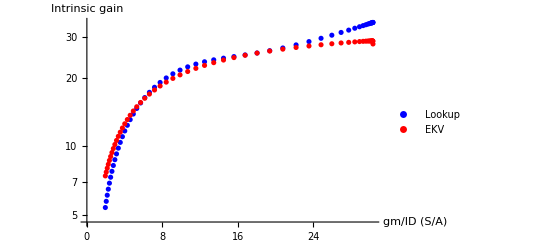

```mathematica
(* =====================================================================
   7. intrinsic gain vs gm/ID — 固定 VDS=0.6V 扫 VGS
   ===================================================================== *)
With[{yy = XTRACT[nch, L, Select[nch["VDS"], .5 <= # <= .7 &], VSB, rho]},
  j = First@Ordering[Abs[Select[nch["VDS"], .5 <= # <= .7 &] - 0.6], 1];
  nJ = yy[[j, 2]]; dnJ = yy[[j, 5]]; dvtJ = yy[[j, 6]]; djsJ = yy[[j, 7]];
  gmidLut = lookup[nch, "GM_ID", "L", L, "VGS", vgs, "VDS", 0.6, "VSB", VSB];
  qG = Map[Max[1/(nJ*UT*#) - 1, $MachineEpsilon] &, gmidLut];
  xG = 2 (qG - 1) + Log[qG];
  gainLut = lookup[nch, "GAIN", "L", L, "VGS", vgs, "VDS", 0.6, "VSB", VSB];
  gainEkv = 1/(djsJ/gmidLut - dvtJ - xG*dnJ);
  ListLogPlot[{Transpose[{gmidLut, gainLut}], Transpose[{gmidLut, gainEkv}]},
   PlotStyle -> {Blue, {Red, Dashed}}, PlotLegends -> {"Lookup", "EKV"},
   AxesLabel -> {"gm/ID (S/A)", "Intrinsic gain"}, GridLines -> Automatic]
]
```